```mathematica
Solve[{x11+x12+x22 ==1, x11 + (1/2)*x12==x1,  x22 + (1/2)*x12==1-x1, x11 == (x11*(1-delta) + (1/2)*x12*(1/(1+delta)) )/((x11+x22)*(1-delta) + x12 * (1/(1+delta)))^2},{x11,x12,x22}]
```

{{x11→(delta^2-delta^4+2 delta^4 x1)/(3 delta^4)-(-4 delta^4+20 delta^6+12 delta^7-4 delta^8-16 delta^6 x1+16 delta^8 x1-16 delta^8 x1^2)/(6 2^(2/3) delta^4 (21+√1)^(1/3))+((21+√(4 1^3+1))^(1/3))/(12 2^(1/3) delta^4),x12→1,x22→2/3+12+1+(1)^(1/3)/(12 2^1 delta^4)},{1},{1}}
 |  |  |  |

```mathematica
delta = 0.8;Solve[{x11+x12+x22 ==1, x11 + (1/2)*x12==x1,  x22 + (1/2)*x12==1-x1, x11 == (x11*(1-delta) + (1/2)*x12*(1/(1+delta)) )/((x11+x22)*(1-delta) + x12 * (1/(1+delta)))^2},{x11,x12,x22}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x11→0.0208333 (9.+32. x1)+((5.08626×10^-6-8.80967×10^-6 ⅈ) (2.1289×10^6-589824. x1-1.04858×10^6 x1^2))/(-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3)-(0.00520833+0.0090211 ⅈ) (-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3),x12→-0.375+0.666667 x1-(21.6563-37.5097 ⅈ)/(-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3)+((6.-10.3923 ⅈ) x1)/(-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3)+((10.6667-18.4752 ⅈ) x1^2)/(-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3)+(0.0104167+0.0180422 ⅈ) (-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3),x22→1.1875-1.33333 x1+(10.8281-18.7549 ⅈ)/(-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3)-((3.-5.19615 ⅈ) x1)/(-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3)-((5.33333-9.2376 ⅈ) x1^2)/(-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3)-(0.00520833+0.0090211 ⅈ) (-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3)},{x11→0.0208333 (9.+32. x1)+((5.08626×10^-6+8.80967×10^-6 ⅈ) (2.1289×10^6-589824. x1-1.04858×10^6 x1^2))/(-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3)-(0.00520833-0.0090211 ⅈ) (-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3),x12→-0.375+0.666667 x1-(21.6563+37.5097 ⅈ)/(-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3)+((6.+10.3923 ⅈ) x1)/(-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3)+((10.6667+18.4752 ⅈ) x1^2)/(-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3)+(0.0104167-0.0180422 ⅈ) (-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3),x22→1.1875-1.33333 x1+(10.8281+18.7549 ⅈ)/(-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3)-((3.+5.19615 ⅈ) x1)/(-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3)-((5.33333+9.2376 ⅈ) x1^2)/(-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3)-(0.00520833-0.0090211 ⅈ) (-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3)},{x11→0.0208333 (9.+32. x1)-(0.0000101725 (2.1289×10^6-589824. x1-1.04858×10^6 x1^2))/(-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3)+0.0104167 (-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3),x12→-0.375+0.666667 x1+43.3125/(-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3)-(12. x1)/(-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3)-(21.3333 x1^2)/(-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3)-0.0208333 (-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3),x22→1.1875-1.33333 x1-21.6563/(-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3)+(6. x1)/(-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3)+(10.6667 x1^2)/(-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3)+0.0104167 (-59049.+270864. x1-27648. x1^2-32768. x1^3+418.282 √(71289.-225522. x1+373936. x1^2-22528. x1^3-65536. x1^4))^(1/3)}}

```mathematica
Solve[{(b11)*x11==(((x11*b11+0.5*x12*b12)*(x11*b11+0.5*x12*b12))/((x11*b11+x12*b12+x22*b22)))},x11]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x11→(0.25 b12^2 x12^2)/(b11 b22 x22)}}

```mathematica
(*Solve[{(b11)*x11==(((x11*b11+(1/2)*x12*b12)*(x11*b11+(1/2)*x12*b12))/((x11*b11+x12*b12+x22*b22)))},x11]
```

```mathematica
Solve[{b11==1-d, b12 ==  1/(1+d), b22 ==  1-d, x11 +(1/2)x12== x1, x2 == x22 + (1/2)*(x12), x1 == 1-x2,(b11)*x11==(((x11*b11+(1/2)*x12*b12)*(x11*b11+(1/2)*x12*b12))/((x11*b11+x12*b12+x22*b22)))},x11]
```

{}

```mathematica
Solve[{ (1-d)*x11==(((x11*(1-d)+(1/2)*(2(x1-x11))*( 1/(1+d)))*(x11*(1-d)+(1/2)*(2(x1-x11))*( 1/(1+d))))/((x11*(1-d)+(2(x1-x11))*( 1/(1+d))+(1-x11-(2(x1-x11)))*(1-d))))},x11]
```

{{x11→1/(2 (2 d^2-d^4))(1-2 d^2+d^4+4 d^2 x1-2 d^4 x1-(-1+d^2) √(1-2 d^2+d^4+8 d^2 x1-4 d^4 x1-8 d^2 x1^2+4 d^4 x1^2))},{x11→1/(2 (2 d^2-d^4))(1-2 d^2+d^4+4 d^2 x1-2 d^4 x1+(-1+d^2) √(1-2 d^2+d^4+8 d^2 x1-4 d^4 x1-8 d^2 x1^2+4 d^4 x1^2))}}

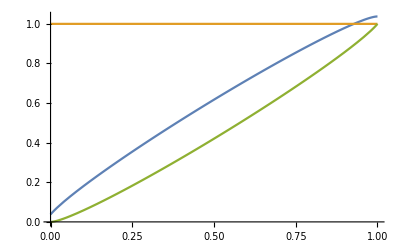

```mathematica
d=.9;Plot[{1/(2 (2 d^2-d^4))(1-2 d^2+d^4+4 d^2 x1-2 d^4 x1-(-1+d^2) √(1-2 d^2+d^4+8 d^2 x1-4 d^4 x1-8 d^2 x1^2+4 d^4 x1^2)),1,1/(2 (2 d^2-d^4))(1-2 d^2+d^4+4 d^2 x1-2 d^4 x1+(-1+d^2) √(1-2 d^2+d^4+8 d^2 x1-4 d^4 x1-8 d^2 x1^2+4 d^4 x1^2))},{x1,0,1}]
```

```mathematica
Solve[{ (1-d)*x11==(((x11*(1-d)+(1/2)*(2(x1-x11))*( 1/(1+d)))*(x11*(1-d)+(1/2)*(2(x1-x11))*( 1/(1+d))))/((x11*(1-d)+(2(x1-x11))*( 1/(1+d))+(1-x11-(2(x1-x11)))*(1-d))))},x1]
```

{{x1→2 d^2 x11-d^4 x11-√(x11-2 d^2 x11+d^4 x11-2 d^2 x11^2+5 d^4 x11^2-4 d^6 x11^2+d^8 x11^2)},{x1→2 d^2 x11-d^4 x11+√(x11-2 d^2 x11+d^4 x11-2 d^2 x11^2+5 d^4 x11^2-4 d^6 x11^2+d^8 x11^2)}}

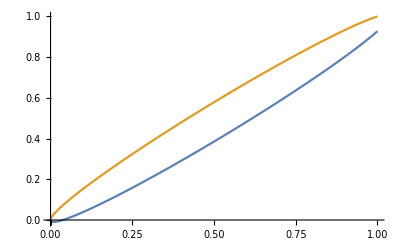

```mathematica
d=0.9;Plot[{2 d^2 x11-d^4 x11-√(x11-2 d^2 x11+d^4 x11-2 d^2 x11^2+5 d^4 x11^2-4 d^6 x11^2+d^8 x11^2), 2 d^2 x11-d^4 x11+√(x11-2 d^2 x11+d^4 x11-2 d^2 x11^2+5 d^4 x11^2-4 d^6 x11^2+d^8 x11^2)},{x11,0,1}]
```